```mathematica
<<TimeSeriesManipulation`;
```

```mathematica
s1=FinancialData["C","2008"];s2=FinancialData["GS","2008"];
```

```mathematica
Latest[s1,3]
```

{{{2009,3,17},2.51},{{2009,3,18},3.08},{{2009,3,19},2.6}}

```mathematica
TimeSeriesTake[s1,{"2008/1","2008/1/31"}]
```

{{{2008,1,2},27.34},{{2008,1,3},27.35},{{2008,1,4},26.69},{{2008,1,7},26.71},{{2008,1,8},25.65},{{2008,1,9},25.99},{{2008,1,10},26.57},{{2008,1,11},27.},{{2008,1,14},27.47},{{2008,1,15},25.47},{{2008,1,16},24.8},{{2008,1,17},23.59},{{2008,1,18},23.11},{{2008,1,22},23.06},{{2008,1,23},24.92},{{2008,1,24},25.83},{{2008,1,25},25.18},{{2008,1,28},26.14},{{2008,1,29},26.38},{{2008,1,30},26.35},{{2008,1,31},26.94}}

#### TimeSeriesAlign

Align two time series based on their dates, dropping date points that are not common:

```mathematica
TimeSeriesAlign[{{{d1, 1}, {d2,2},{d3,3}},{{d2,2},{d3,3},{d4,4}}}]
```

{{{d2,2},{d3,3}},{{d2,2},{d3,3}}}

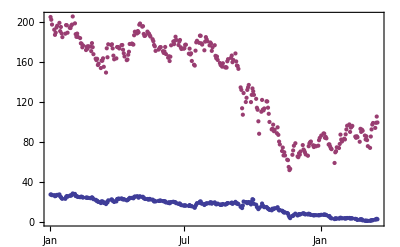

```mathematica
TimeSeriesAlign[{FinancialData["C","2007"],FinancialData["GS","2008"]}]//DateListPlot
```

#### TimeSeriesMap

Map a function on the values of a time series, keeping the dates:

```mathematica
TimeSeriesMap[f,{{d1, 1}, {d2,2},{d3,3}}]
```

{{d1,f[1]},{d2,f[2]},{d3,f[3]}}

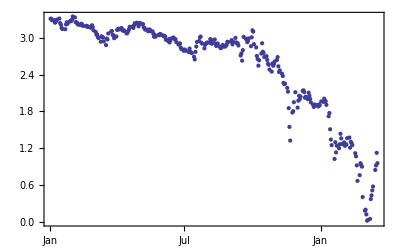

```mathematica
TimeSeriesMap[Log,s1]//DateListPlot
```

#### TimeSeriesMapThread

Map a multi-argument function over multiple time series, e.g., get the ratio of the prices of two assets:

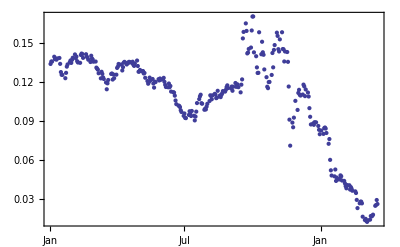

```mathematica
TimeSeriesMapThread[#1/#2&,{s1,s2}]//DateListPlot
```

### TimeSeriesDifferences / TimeSeriesRatios

Get differences / ratios of a time series. By convention, the difference is assigned to the most recent date.

```mathematica
TimeSeriesDifferences[{{d1, 1}, {d2,2},{d3,3}}]
```

{{d2,1},{d3,1}}

```mathematica
TimeSeriesRatios[{{d1, 1}, {d2,2},{d3,3}}]
```

{{d2,2},{d3,3/2}}

#### TimeSeriesMovingAverage / TimeSeriesMovingMedian

Moving averages and medians over a given window:

```mathematica
TimeSeriesMovingAverage[{{d1, 1}, {d2,2},{d3,3}},2]
```

{{d2,3/2},{d3,5/2}}

```mathematica
TimeSeriesMovingMedian[{{d1, 1}, {d2,2},{d3,3}},2]
```

{{d2,3/2},{d3,5/2}}

Get the 30-day moving average for a stock:

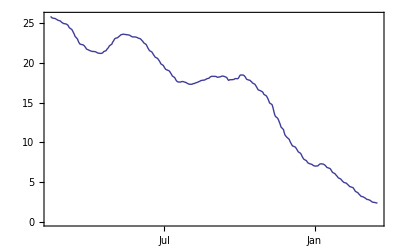

```mathematica
DateListPlot[TimeSeriesMovingAverage[s1,30],Joined->True]
```

Vary the moving average window to get a smoother picture:

```mathematica
Manipulate[DateListPlot[TimeSeriesMovingAverage[s1,window],Joined->True],{window,1,30,1}]
```

DateListPlot::ntdt: The first argument to DateListPlot should be a list of pairs of dates and real values, a list of real values, or a list of several such lists.

ListConvolve::kldims: The kernel {1} and list s1 are not both non-empty lists with the same tensor rank.

DateListPlot::ntdt: The first argument to DateListPlot should be a list of pairs of dates and real values, a list of real values, or a list of several such lists.

#### Generalization: TimeSeriesMovingMap

Generalization of MovingAverage: instead of Mean, apply an arbitrary function to the values within a window:

```mathematica
TimeSeriesMovingMap[Min,{{d1, 1}, {d2,2},{d3,3}},2]
```

{{d2,1},{d3,2}}

Moving average and Min/Max band for 30 days

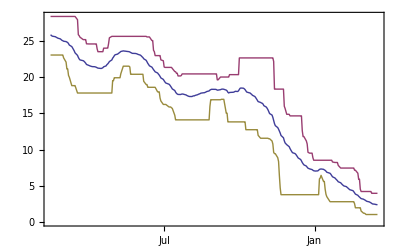

```mathematica
DateListPlot[{TimeSeriesMovingAverage[s1,30],TimeSeriesMovingMap[Max,s1,30],TimeSeriesMovingMap[Min,s1,30]},Joined->True]
```

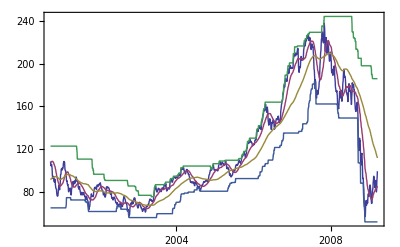

```mathematica
With[{s1=FinancialData[ "GS","2000"]},DateListPlot[TimeSeriesAlign@{TimeSeriesMovingAverage[s1,5],TimeSeriesMovingAverage[s1,50],TimeSeriesMovingAverage[s1,180],TimeSeriesMovingMap[Max,s1,180],TimeSeriesMovingMap[Min,s1,180]},Joined->True]]
```

#### FurtherGeneralization: TimeSeriesListConvolve and TimeSeriesListCorrelate:

These functions work like ListConvolve and ListCorrelate with the full set of arguments, only they keep the date annotation:

```mathematica
TimeSeriesListConvolve[{x,y},{{d1, 1}, {d2,2},{d3,3}}]
```

{{d2,2 x+y},{d3,3 x+2 y}}

```mathematica
TimeSeriesListCorrelate[{x,y},{{d1, 1}, {d2,2},{d3,3}}]
```

{{d2,x+2 y},{d3,2 x+3 y}}

#### TimeSeriesFoldList / TimeSeriesAccumulate

Fold/FoldList cousins. Note that instead of taking an arbitrary value as a start value, these functions take the first element of the list as a starting value.

```mathematica
TimeSeriesFoldList[Times,{{d1, 1}, {d2,2},{d3,3}}]
```

{{d1,1},{d2,2},{d3,6}}

```mathematica
TimeSeriesAccumulate[{{d1, 1}, {d2,2},{d3,3}}]
```

{{d1,1},{d2,3},{d3,6}}

```mathematica
OrderedQ
```

```mathematica
Attributes[AbsoluteTime]
```

{Protected}

#### TimeSeriesInterpolate

```mathematica
foo=TimeSeriesInterpolation[s1]
```

Function[time$,InterpolatingFunction[{{3.40822×10^9,3.4465×10^9}},<>][AbsoluteTime[time$]]]

```mathematica
AbsoluteTime[{1900,1,1}]
```

0

```mathematica
{"Year"->1,"Month"->2,"Day"->3,"Hour"->4,"Minute"->5,"Second"->6}[[All,1]]
```

{Year,Month,Day,Hour,Minute,Second}

```mathematica
AbsoluteTime[DatePlus[{1900,1,1},{1,"Week"}]]
```

604800

```mathematica
DateList[1000.001]
```

{1900,1,1,0,16,40.001}

```mathematica
AbsoluteTime[DatePlus[{1900,1,1},{1,"Year"}]]/AbsoluteTime[DatePlus[{1900,1,1},{1,"Week"}]]//N
```

52.1429

```mathematica
foo["2008/7/1"]
```

16.59

```mathematica
DateRange[{2008,1,1},{2008,10,2},{1,"Month"}]
```

{{2008,1,1},{2008,2,1},{2008,3,1},{2008,4,1},{2008,5,1},{2008,6,1},{2008,7,1},{2008,8,1},{2008,9,1},{2008,10,1}}

```mathematica
NestWhileList
```

```mathematica
NestWhileList
```

```mathematica
{#,foo@#}&/@DatePlusList["2008/1/10",{10,"Week"}]//DateListPlot
```

```mathematica
AbsoluteTime/@s1[[{1,-1},1]]
```

{3408220800,3446496000}

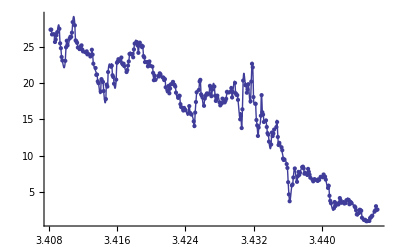

```mathematica
Show[{ListPlot[TimeSeriesDateMap[AbsoluteTime,s1]],Plot[foo@DateList@x,{x,3408220800,3446496000}]}]
```

```mathematica
DateListPlot[
```

```mathematica
<<TimeSeriesManipulation`
```